levelset[e_,k_]:=Module[{k1,set1},k1=k;set1=ContourPlot[e==k1,{x,-8,8},{y,-8,8},Axes→True];Return[set1]]
C. Place the answer to a question right after it. 
D. Remember to use alt + 7 to format cells in which you will be typing text. You don’ t need to format cells in which you will be writing Mathematica code.
To submit
E. Save the notebook as yourname_assignment 1.nb
F. Evaluate entire notebook.
G. Save as a .pdf file.
H. Submit to Canvas These are due on Friday, March 11.
## In new cells, experiment by typing and evaluating the following:

        A. Solve[2x=7]
        B. a=9; Solve[2x==a] (that’s a semicolon in there)
        C. a=9 [Return] Solve[2x==a] (the carriage return is not Shift+Return).
        
Sum up what you have deduced about semi-colons, the Solve command, and use of equal signs. In particular, what’s the difference between B and C?
## In new cells, experiment with this by typing and evaluating the following:

      C. Solve [3x==y]
      D. Solve[3x==y,{x}].

Sum up what you have deduced about the Solve command and solving for particular variables.
## What are the pros and cons of using NSolve instead of Solve?
## Play around with the ContourPlot command: use ContourPlot to draw a parabola, a hyperbola, a line, and a cubic, some with and some without axes. 
## Change the bounds on

Show[ContourPlot[(x-1)^2+(y-7)^2==10,{x,-3,5},{y,0,12},Axes→True],ContourPlot[y==3 x^2+1,{x,-3,5},{y,0,12},Axes→True]]

so that the circle comes out looking circular. (You’ll need to cut-and-paste it into a cell that isn’t formatted for text.) Briefly sum up what you think is happening.
## Get Mathematica to draw a picture of a parabola and a line tangent to the parabola at some point other than the vertex. If you want to show off, include a (visible) point of tangency in your picture. (You may need to look up the command “Point” in the documentation under the Help tab.)
## Play a little. Is it the case that every level set for f(x,y)=3xy+2y is a hyperbola? Explain.

## Change the input expression so that the corresponding level set is a parabola. 

## How about two lines intersecting lines? Two parallel lines? The goal here is to only use one levelset command.

## Next change the module itself. Write a module called levelsetwithbounds that takes as input an expression e, a value k and a number M and has as output the level set of f(x,y)=e corresponding to the level k between the ranges -M≤ x,y≤ M. (Our levelset module only draws the picture where M=8.) Use your module to draw a picture of part of parabola containing the vertex where the vertex is more than 40 away from the origin. 
For the next question, you need the following module. Be sure to evaluate it.
log[n_]:=Module[{index},
If[n≤ 0,Return[“Please enter a positive number”],Return[Log10[n]]]
(*This is the If command. It looks like this: 
If[_____,______,______] where the first entry is a condition and the second and third entries are actions. *)
(* It works like this:
If the condition in the first entry holds, it does the thing in the second entry. If the condition doesn’t hold, it does the thing in the third entry.*)
]
## Evaluate the module. Then enter and evaluate the following: 
log[100]
log[100000]
log[13.4]
log[-6]
Explain your results.
## Plug a bunch of different kinds of numbers into the module below (after evaluating it).
ilikeevennumbers[n_]:=Module[{a},a=RandomInteger[2];
If[EvenQ[n],Return[{“Yippee!”,”Wonderful”,”Fantastic”}[[a+1]]]]
]
Explain what the module does.
##  Write a module that takes as input a positive integer m prints the first m positive odd numbers and returns the square root of the sum of the numbers it printed. You should use the Print command in the module. Look it up in the Wolfram Documentation center available under the Help tab.  Run your module for 3 different numbers between 20 and 50. Do you have any thoughts about the output?

```mathematica
Solve[2x=7]
a=9;Solve[2x==a]
a=9[Return]Solve[2x==a]
```

Set::write: Tag Times in 2 x is Protected.

Solve::naqs: 7 is not a quantified system of equations and inequalities.

Solve[7]

{{x→9/2}}

{{9[Return] (x→9/2)}}

I belive that the semi-colon is used to supress output so that a variable can be declared and an expression contanining said variable can be evaluated on the same line. The solve command seems pretty self explanitory, it evaluates an equation. Equal signs on their own appear to be declaring a variable whereas double equal signs denote an equality to be evaluated. In the second bit of code we are evaluating expressions where a variable is defined, in one the variable is declared by a single = sign and supressed by a semicolen, in the next the variable is returned in addition to the solution to the equality.

```mathematica
Solve[3x==y]
Solve[3x==y,{x}]
```

{{y→3 x}}

{{x→y/3}}

My deductions about the Solve command have not changed since the problem I answered one minute ago. However, I have learned that including in the solve brackets a comma followed by one of the variables in squiggly brackets appears to be the syntax for telling Mathematica which variable you would like it to evaluate the expression for.

```mathematica
Solve[x^2==5]
NSolve[x^2==5]
```

{{x→-√5},{x→√5}}

{{x→-2.23607},{x→2.23607}}

```mathematica
NSolve[y==3x^2+1&&(x-1)^2+(y-7)^2==10,{x,y}]
Solve[y==3x^2+1&&(x-1)^2+(y-7)^2==10,{x,y}]
```

{{x→-1.61082,y→8.78426},{x→1.73922,y→10.0747},{x→-1.10099,y→4.63657},{x→0.972598,y→3.83784}}

{{x→-1/6 √(1/3 (70+4141/(263791+18 ⅈ √4394085)^(1/3)+(263791+18 ⅈ √4394085)^(1/3)))-1/2 √(140/27-4141/(27 (263791+18 ⅈ √4394085)^(1/3))-1/27 (263791+18 ⅈ √4394085)^(1/3)-4/(√(3 (70+4141/(263791+18 ⅈ √4394085)^(1/3)+(263791+18 ⅈ √4394085)^(1/3))))),y→41/6-1/(√(1/3 (70+4141/(263791+18 ⅈ √4394085)^(1/3)+(263791+18 ⅈ √4394085)^(1/3))))+1/2 √(1/3 (70+4141/(263791+18 ⅈ √4394085)^(1/3)+(263791+18 ⅈ √4394085)^(1/3))) √(140/27-4141/(27 (263791+18 ⅈ √4394085)^(1/3))-1/27 (263791+18 ⅈ √4394085)^(1/3)-4/(√(3 (70+4141/(263791+18 ⅈ √4394085)^(1/3)+(263791+18 ⅈ √4394085)^(1/3)))))},{x→-1/6 √(1/3 (70+4141/(263791+18 ⅈ √4394085)^(1/3)+(263791+18 ⅈ √4394085)^(1/3)))+1/2 √(140/27-4141/(27 (263791+18 ⅈ √4394085)^(1/3))-1/27 (263791+18 ⅈ √4394085)^(1/3)-4/(√(3 (70+4141/(263791+18 ⅈ √4394085)^(1/3)+(263791+18 ⅈ √4394085)^(1/3))))),y→41/6-1/(√(1/3 (70+4141/(263791+18 ⅈ √4394085)^(1/3)+(263791+18 ⅈ √4394085)^(1/3))))-1/2 √(1/3 (70+4141/(263791+18 ⅈ √4394085)^(1/3)+(263791+18 ⅈ √4394085)^(1/3))) √(140/27-4141/(27 (263791+18 ⅈ √4394085)^(1/3))-1/27 (263791+18 ⅈ √4394085)^(1/3)-4/(√(3 (70+4141/(263791+18 ⅈ √4394085)^(1/3)+(263791+18 ⅈ √4394085)^(1/3)))))},{x→1/6 √(1/3 (70+4141/(263791+18 ⅈ √4394085)^(1/3)+(263791+18 ⅈ √4394085)^(1/3)))-1/2 √(140/27-4141/(27 (263791+18 ⅈ √4394085)^(1/3))-1/27 (263791+18 ⅈ √4394085)^(1/3)+4/(√(3 (70+4141/(263791+18 ⅈ √4394085)^(1/3)+(263791+18 ⅈ √4394085)^(1/3))))),y→41/6+1/(√(1/3 (70+4141/(263791+18 ⅈ √4394085)^(1/3)+(263791+18 ⅈ √4394085)^(1/3))))-1/2 √(1/3 (70+4141/(263791+18 ⅈ √4394085)^(1/3)+(263791+18 ⅈ √4394085)^(1/3))) √(140/27-4141/(27 (263791+18 ⅈ √4394085)^(1/3))-1/27 (263791+18 ⅈ √4394085)^(1/3)+4/(√(3 (70+4141/(263791+18 ⅈ √4394085)^(1/3)+(263791+18 ⅈ √4394085)^(1/3)))))},{x→1/6 √(1/3 (70+4141/(263791+18 ⅈ √4394085)^(1/3)+(263791+18 ⅈ √4394085)^(1/3)))+1/2 √(140/27-4141/(27 (263791+18 ⅈ √4394085)^(1/3))-1/27 (263791+18 ⅈ √4394085)^(1/3)+4/(√(3 (70+4141/(263791+18 ⅈ √4394085)^(1/3)+(263791+18 ⅈ √4394085)^(1/3))))),y→41/6+1/(√(1/3 (70+4141/(263791+18 ⅈ √4394085)^(1/3)+(263791+18 ⅈ √4394085)^(1/3))))+1/2 √(1/3 (70+4141/(263791+18 ⅈ √4394085)^(1/3)+(263791+18 ⅈ √4394085)^(1/3))) √(140/27-4141/(27 (263791+18 ⅈ √4394085)^(1/3))-1/27 (263791+18 ⅈ √4394085)^(1/3)+4/(√(3 (70+4141/(263791+18 ⅈ √4394085)^(1/3)+(263791+18 ⅈ √4394085)^(1/3)))))}}

The pros of Nsolve are that it produces decimal output and is therefore more simple to understand and digest as well as taking up less physical or virtual space to display. The con is that Nsolve is not an exact expression of the solution but rather an approximation.

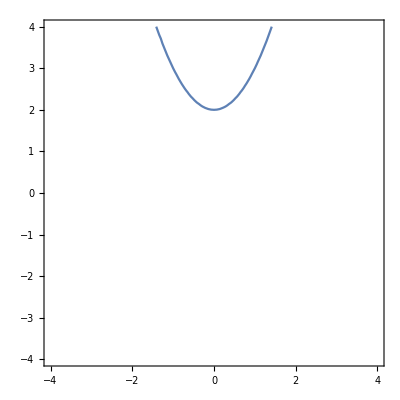

```mathematica
ContourPlot[y==x^2+2,{x,-4,4},{y,-4,4},Axes->True]
```

```mathematica
ContourPlot[y==3x+1,{x,-4,4},{y,-4,4},Axes->False]
```

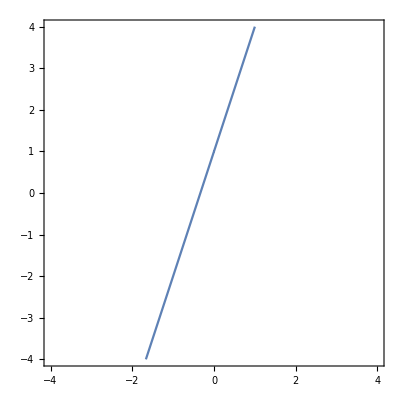

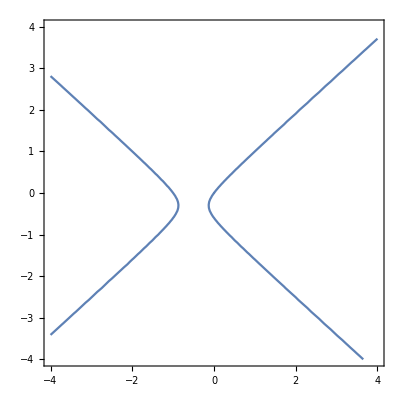

```mathematica
ContourPlot[4x^2-5y^2+4x-3y==0,{x,-4,4},{y,-4,4},Axes->True]
```

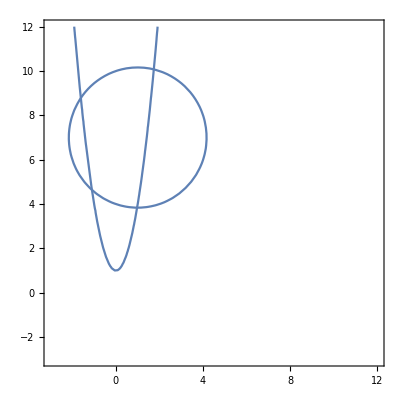

```mathematica
Show[ContourPlot[(x-1)^2+(y-7)^2==10,{x,-3,12},{y,-3,12},Axes->True],ContourPlot[y==3x^2+1,{x,-3,12},{y,-3,12},Axes->True]]
```

I changed the bounds so that the X-bound and the Y-bound were identical in order to counteract the streching effect seen in the original example.

1+3 x^2

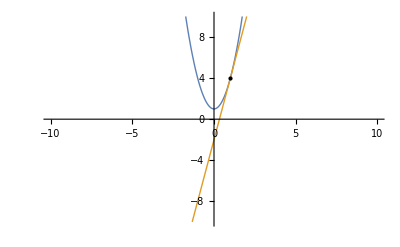

```mathematica
f[x_]=3x^2+1
With[{a=1},Plot[{f[x],f'[a](x-a)+f[a]},{x,-10,10},PlotRange->{-10,10},PlotStyle->Thick,Epilog->{PointSize[Large],Point[{a,f[a]}]}]]
```

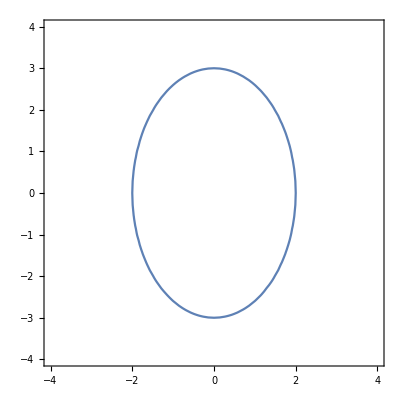

```mathematica
ContourPlot[9x^2+4y^2==36,{x,-4,4},{y,-4,4},Axes->True]
```

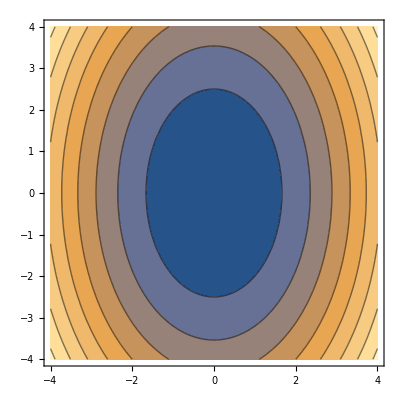

```mathematica
ContourPlot[9x^2+4y^2,{x,-4,4},{y,-4,4},Axes->True]
```

```mathematica
levelset[e_,k_]:=Module[{k1,set1},k1=k;set1=ContourPlot[e==k1,{x,-8,8},{y,-8,8},Axes->True];Return[set1]]
levelset[3 x y +2 y, 1]
```

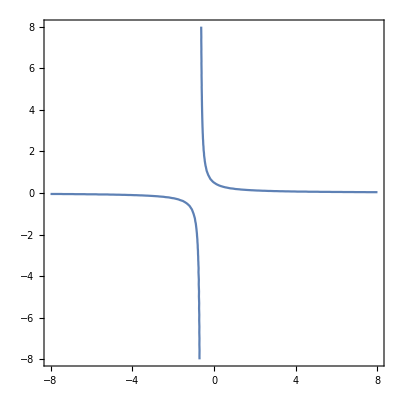
```mathematica
-Graphics-
levelset[3 x y +2 y,0]
```

-Graphics-

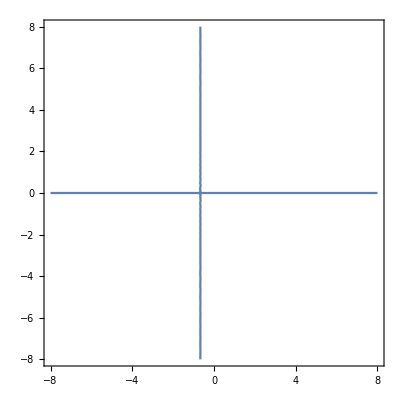

It is not the case that every level set for f(x,y)=3xy+2y is a hyperbola, when you set the constant “k”=0 the level set becomes an orthogonal intersection of lines parallel to the x and y axis rather than a hyperbola.

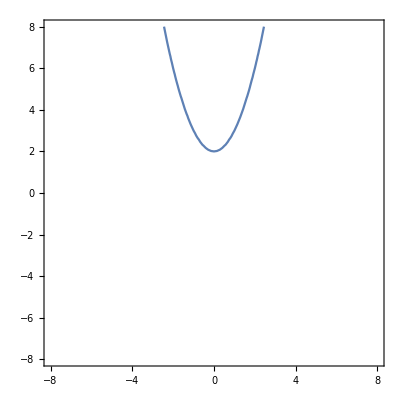

```mathematica
levelset[e_,k_]:=Module[{k1,set1},k1=k;set1=ContourPlot[e==k1,{x,-8,8},{y,-8,8},Axes->True];Return[set1]]
levelset[ y-x^2, 2]
```

```mathematica
levelset[e_,k_]:=Module[{k1,set1},k1=k;set1=ContourPlot[e==k1,{x,-8,8},{y,-8,8},Axes->True];Return[set1]]
levelset[x y ,0]
```

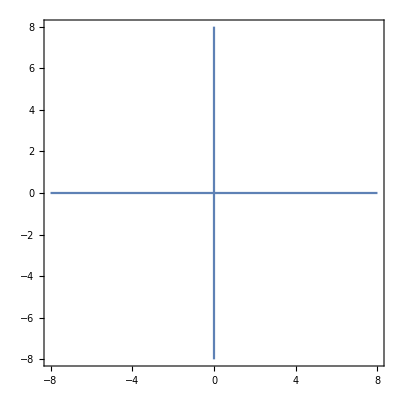
```mathematica
-Graphics-
levelset[-.5 x- .5y ,1]
```

-Graphics-

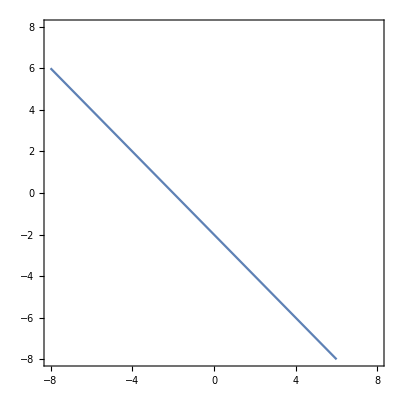

Return[set1]

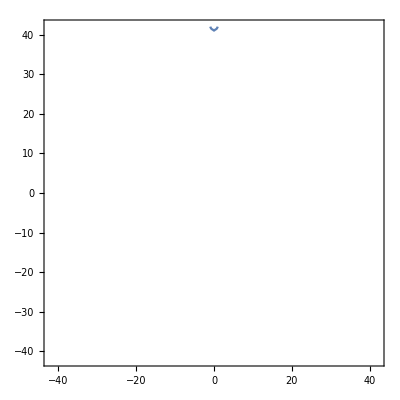

While::argt: While called with 3 arguments; 1 or 2 arguments are expected.

Set::write: Tag Times in 2 set1$25144 While[-m1$25144≤x,y≤m1$25144,k1$25144≤abs[40]] is Protected.

```mathematica
levelsetwithbounds[e_,k_,m_]:=Module[{k1,set1},k1=k;

set1=ContourPlot[e==k1,{x,-m,m},{y,-m,m},Axes->True]];
Return[set1]

levelsetwithbounds[y-x^2,41,42]
```

```mathematica
log[n_]:=Module[{index},
If[n≤ 0,Return["5"],Return[Log10[n]]]
]
log[n]
```

If[n≤0,Return[5],Return[Log10[n]]]

```mathematica
log[100]
```

2

```mathematica
log[100000]
```

5

```mathematica
log[13.4]
```

1.1271

```mathematica
log[-6]
```

5

The Module worked as expected, it took the base 10 log of each input, in the case of log[100000] the solution happens by coincidence to be 5 but in the case of -6 the output is 5 because of the If[n<=0,Return[“5”]] condition.

```mathematica
ilikeevennumbers[n_]:=Module[{a},a=RandomInteger[2];
If[EvenQ[n],Return[{"Yippee!","Wonderful","Fantastic"}[[a+1]]]]
]
ilikeevennumbers[n]
```

```mathematica
ilikeevennumbers[2]
```

Yippee!

```mathematica
ilikeevennumbers[3]
```

```mathematica
ilikeevennumbers[4]
ilikeevennumbers[6]
ilikeevennumbers[8]
ilikeevennumbers[20]
```

Fantastic

Wonderful

Yippee!

Fantastic

This Module takes an integer input, if it finds it to be an odd number it does not react however if it detects an even number it returns 1 of three phrases starting with “yipee!”, each subsequent time it detects an even number a random integer between 0 and 2 is generated and added to 1 corresponding to the phrases positions, because 1 is added every time this process occurs, the process must occur 3 times for any phrase to be reused.

```mathematica
sumofsquares[n_]:=Module[{index,sum},index=1;sum=0;
If[Or[n≤ 0,IntegerQ[n]==False],Return["Please enter a positive integer"]];
While[index≤n,sum=sum+index^2;index=index+1];
Return[sum]]
sumofsquares[n]
```

Please enter a positive integer

```mathematica
sumofsquares[1]
```

1

```mathematica
sumofsquares[2]
```

5

```mathematica
sumofsquares[3]
```

14

```mathematica
sumofsquares[5]
```

55

```mathematica
sumofsquares[100]
```

338350

```mathematica
positiveint[m_Integer?(Positive@#&)]:=(Print@#;Sqrt@Tr@#)&@Range[1,2 m-1,2]

squarerootofsum[m_]=Module[{index,sum},index=0;sum=0;
If[Or[m≤0,IntegerQ[m]==False],Return["Please enter a positive integer"]];
While[index≤m,sum=Sqrt[Sum[positiveint[m_Integer?(Positive@#&)]{0,m};]index=index+1;]

Return[sum]]]


squarerootofsum[34]
```

Return[Please enter a positive integer]

Please enter a positive integer